```mathematica
ClearAll["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
MyExportPDF[file_,figure_]:= Module[{outlinedGraphics},
outlinedGraphics=First@ImportString[ExportString[figure,"PDF"],"PDF","TextMode"->"Outlines"];
Export[file,outlinedGraphics];
]

Get["jlabColors`"]
Get["boxPlot`"]
Get["Spec743`"]
ColorSetter /@ jlabColorTable 

BRRad = 10; 
Bscatter = 30; 
Bxst = 1; 
Bxw = 100; 
Binc = 0; 
Bstep = 230; 
PrL = 1400; 
PrH = 3300;
```

{0.7529411764705882,0.9764705882352941,0.1843137254901961,0.2549019607843137,0.8980392156862745,0.5019607843137255,0.49019607843137253}

```mathematica
Λ^PG=Λ^(-+)
```

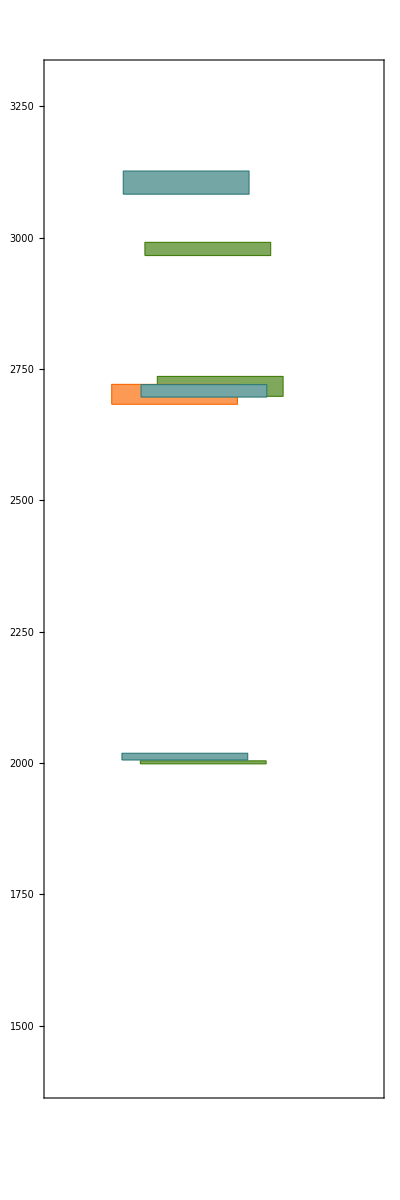

```mathematica
RRad = BRRad; 
scatter = Bscatter; 
xst = Bxst; 
xw = Bxw; 
inc = Binc; 
step = Bstep; 


T2mP = boxStack[ PT2mP[RRad,scatter,xst+inc*step,xw] ];++inc; 


ThePlotmP = Show[ T2mP,
	PlotRange->{{xst- 0.5*step,xst + (inc-0.5)*step+scatter}, {PrL,PrH}}, 
	Axes->False,
	Frame->{{True,True},{False,False}},
	FrameTicks->{{All,All},{None,None}},
	AspectRatio->3];
Magnify[ ThePlotmP, 4]
MyExportPDF[ "BoxPlotUnlabeledmP.pdf" , ThePlotmP ]
```